# Ice Melting under a lamp

## This Demonstration uses data collected in lab to show instantaneous rates of change in ice melt

## First we assign these data to a set, This is the beaker from by the window

```mathematica
Data={{0,0,500,0},{15,7,493,7/500//N},{30,29,471,22/493//N},{45,55,445,26/471//N}}
```

{{0,0,500,0},{15,7,493,0.014},{30,29,471,0.0446247},{45,55,445,0.0552017}}

## Then we graph the data to get an understanding of its tendency

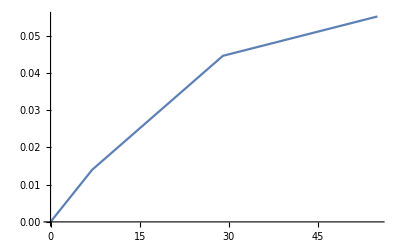

```mathematica
ListLinePlot[Map[Drop[##,{1,3,2}]&,Data]]
```

## We define a second order polynomial using the amount of melted water, and the rate of change

```mathematica
Clear[y]
y[x_]=Fit[Map[Drop[##,{1,3,2}]&,Data],{1,x,x^2},x]
```

0.0000236831+0.00213564 x-0.0000205904 x^2

## Below, we can play with the data to see how the melt rate, while increasing, is slowing down

### In general, using the amount of water, the rate of change is decreasing in a linear fashion, due to the second order polynomial

```mathematica
Manipulate[{y[mil],y'[mil]},{mil},{mil,0,55,1}]
```

```mathematica
Clear[y]
y[x_]:=Sin[x]
```

```mathematica
Manipulate[Show[Plot[y[x],{x,0,4π},PlotLabel->"Sin(x)"],Plot[y[a]+y'[a](x-a),{x,0,4π},PlotStyle->Red]],{a},{a,0,4π,π/8}]
```

## We must use a third order polynomial to show the change of melt rate according to time. The use of a second order polynomial results in the melt rate increasing beyond 5.5%

```mathematica
Clear[f]
f[t_]=Fit[Map[Drop[##,{2,3}]&,Data],{1,t,t^2,t^3},t]
```

2.08943×10^-17-0.00043577 t+0.000118438 t^2-1.81099×10^-6 t^3

## Below, we can see that the melt rate increases, until around 22 minutes, when it begins decreasing

```mathematica
Manipulate[{f[t],f'[t]},{t},{t,0,45,1}]
```

```mathematica
Manipulate[Show[Plot[f[a],{a,0,45},PlotLabel->"Melt Rate vs. Time",AxesLabel->{"Time","Melted Water"}],Plot[f[t]+f'[t](a-t),{a,0,45},PlotStyle->Red]],{t,0,45,1}]
```

## Now we use the data from the beaker in the middle of the room

```mathematica
Data2={{0,0,500,0},{15,9,491,9/500//N},{30,35,465,26/491//N},{45,59,441,24/465//N}}
```

{{0,0,500,0},{15,9,491,0.018},{30,35,465,0.0529532},{45,59,441,0.0516129}}

## It shows that at a certain point, the melt rate begins to decrease

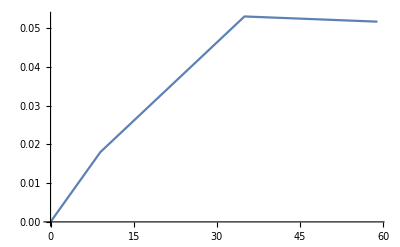

```mathematica
ListLinePlot[Map[Drop[##,{1,3,2}]&,Data2]]
```

## Using a third order polynomial, as a second order polynomial will not work in this instance

```mathematica
Clear[mrvtm]
mrvtm[x_]=Fit[Map[Drop[##,{1,3,2}]&,Data2],{1,x,x^2,x^3},x]
```

-1.37891×10^-17+0.0021191 x-0.0000118187 x^2-1.57138×10^-7 x^3

## The decrease in rate of change is consistent, as with the data from set one

```mathematica
Manipulate[{mrvtm[mil],mrvtm'[mil]},{mil},{mil,0,59,1}]
```

```mathematica
Manipulate[Show[Plot[mrvtm[x],{x,0,59},PlotLabel->"Melt Rate vs. melted water",AxesLabel->{"Water","Melt Rate"}],Plot[mrvtm[mil]-mrvtm'[mil](mil-x),{x,0,59},PlotStyle->Red]],{mil},{mil,0,59,1}]
```

## Establishing a third order polynomial for melt rate vs. time

```mathematica
Clear[mrvst]
mrvst[t_]=Fit[Map[Drop[##,{2,3}]&,Data2],{1,t,t^2,t^3},t]
```

1.95013×10^-17-0.000548362 t+0.000155999 t^2-2.62946×10^-6 t^3

## Begins decreasing in rate of change around time 20

```mathematica
Manipulate[{mrvst[t],mrvst'[t]},{t},{t,0,45,1}]
```

```mathematica
Manipulate[Show[Plot[mrvst[x],{x,0,45},PlotLabel->"Melt Rate vs. Time",AxesLabel->{"Time","Melt Rate"}],Plot[mrvst[t]-mrvst'[t](t-x),{x,0,45},PlotStyle->Red]],{t},{t,0,45,1}]
```